```mathematica
bellman[s_,a_,V_,p_]:=p*V[[Min[Length@V,(s+a)]]]+(1-p)*V[[Max[1,(s-a)]]];
```

```mathematica
stateUpdate[ix_]:=Module[{vix,six,bets,Q,maxQ,pos},

(*get the i'th state*)
six=states[[ix+1]];

(*compute valid bets/actions for this state*)
bets=Range[1,Min[six,goal-six+1]];

(*compute value of each valid action*)
Q=Map[bellman[six,#,valueFunc,pheads]&,bets];

(*determin maximum action/value*)
maxQ=Max@Q;pos=Flatten[Position[Q,maxQ]];

(*return max value and the associated bet size for that max value*)
{maxQ,If[pos==={},0,pos[[1]]]}
];
```

```mathematica
(* win a total of $100 *)
goal=100;

(* probability of coin toss resulting in heads*)
pheads=0.5;

(* init states in units of dollars *)
states=Range[0,100];

(* init value of each state to zero *)
valueFunc=ConstantArray[0,Length@states];

(* terminal state has value 1 *)
valueFunc[[-1]]=1;
```

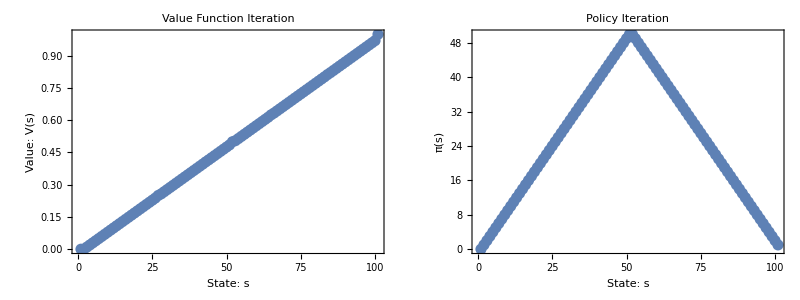

```mathematica
(* compute state value and policy update*)
update=Map[stateUpdate,states];

(* update value function + terminal states *)
valueFunc=update[[;;,1]];valueFunc[[{1,-1}]]={0,1};

(* plot V(s) and π(s) *)
g = Grid[
{{
ListPlot[valueFunc,
ImageSize->Large,
Frame-> True, 
FrameLabel->{
Style["State: s"       ,FontSize->14],
Style["Value: V(s)",FontSize->14]
},
PlotLabel->Style["Value Function Iteration",FontSize->14]
],

ListPlot[update[[;;,2]],
ImageSize->Large,
Frame -> True,
FrameLabel->{
Style["State: s",FontSize->14],
Style["π(s)"         ,FontSize->14]
},
PlotLabel-> Style["Policy Iteration",FontSize->14]
]
}}
]
```

```mathematica
Export["/Users/abelbrown/Dropbox/ReinforcementLearning/GambersProblems.png",g]
```

/Users/abelbrown/Dropbox/ReinforcementLearning/GambersProblems.png